```mathematica
data=Import ["/Users/wanglong/task/32k_2/radius.log","Table"];
```

```mathematica
plotdata=Table[{2*0.117*i,data[[i,4]]},{i,Length[data]}];
```

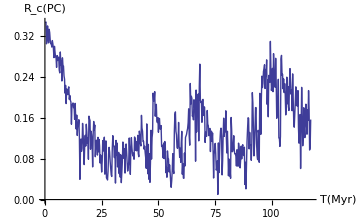

```mathematica
ListPlot[plotdata,Joined->True,AxesLabel->{"T(Myr)","R_c(PC)"}(*,Background->Black,AxesStyle->White,ImageSize->Medium,PlotStyle->White*)]
```

```mathematica
tdata=Table[Import["/Users/wanglong/task/32k_2/t"~~ToString[i],"Table"][[2;;]],{i,0,10,2}];
```

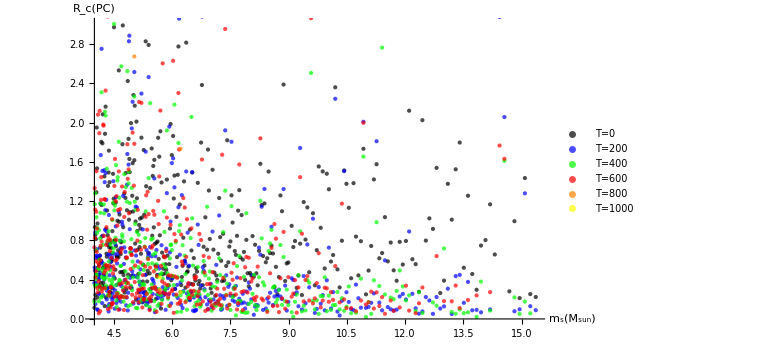

```mathematica
ListPlot[tdata,AxesLabel->{"m_s(M_sun)","R_c(PC)"},Background->White,AxesStyle->Black,ImageSize->Large,PlotRange->{0,3},PlotStyle->({#,Opacity[0.7]}&/@(Reverse@{Yellow,Orange,Red,Green,Blue,Black})),PlotLegends->Placed[{"T=0","T=200","T=400","T=600","T=800","T=1000"},{Right,Center}]]
```

```mathematica
pdata=Import["/Users/wanglong/task/32k_2/out.lst","Table"];
```

```mathematica
t=Table[Select[pdata,#[[1]]==i&],{i,{0,200,400,600,800,1000}}];
terr=Table[Cases[t[[i,All,{2,3,4}]],{x_,y_,ye_}->{{x,-y},ErrorBar[ye]}],{i,Length[t]}];
```

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
ErrorListPlot[terr,PlotStyle->{Orange,Red,Green,Blue,Purple,Black},Joined->True,PlotMarkers->Automatic,PlotLegends->Placed[{"T=0","T=200","T=400","T=600","T=800","T=1000"},{Right,Center}],ImageSize->400,AxesLabel->{"⟨R⟩","α"},LabelStyle->Medium]
```